```mathematica
(*Mathematica*)
```

```mathematica
T[n_,m_,d_]:=If[n==m,2,If[n==d&&m==d-1,-2,If[(n==m-1||n==m+1),-1,0]]]
```

```mathematica
M[d_]:=Table[T[n,m,d],{n,1,d},{m,1,d}]
```

```mathematica
M[10]
```

{{2,-1,0,0,0,0,0,0,0,0},{-1,2,-1,0,0,0,0,0,0,0},{0,-1,2,-1,0,0,0,0,0,0},{0,0,-1,2,-1,0,0,0,0,0},{0,0,0,-1,2,-1,0,0,0,0},{0,0,0,0,-1,2,-1,0,0,0},{0,0,0,0,0,-1,2,-1,0,0},{0,0,0,0,0,0,-1,2,-1,0},{0,0,0,0,0,0,0,-1,2,-1},{0,0,0,0,0,0,0,0,-2,2}}

```mathematica
(*B_10/C_10 Cartan Matrix:or C_n*)
```

```mathematica
B10={{2,-1,0,0,0,0,0,0,0,0},
{-1,2,-1,0,0,0,0,0,0,0},
{0,-1,2,-1,0,0,0,0,0,0},
{0,0,-1,2,-1,0,0,0,0,0},
{0,0,0,-1,2,-1,0,0,0,0},
{0,0,0,0,-1,2,-1,0,0,0},
{0,0,0,0,0,-1,2,-1,0,0},
{0,0,0,0,0,0,-1,2,-1,0},
{0,0,0,0,0,0,0,-1,2,-1},
{0,0,0,0,0,0,0,0,-2,2}}
```

{{2,-1,0,0,0,0,0,0,0,0},{-1,2,-1,0,0,0,0,0,0,0},{0,-1,2,-1,0,0,0,0,0,0},{0,0,-1,2,-1,0,0,0,0,0},{0,0,0,-1,2,-1,0,0,0,0},{0,0,0,0,-1,2,-1,0,0,0},{0,0,0,0,0,-1,2,-1,0,0},{0,0,0,0,0,0,-1,2,-1,0},{0,0,0,0,0,0,0,-1,2,-1},{0,0,0,0,0,0,0,0,-2,2}}

```mathematica
WeightedAdjacencyGraph[B10]
```

```mathematica
Det[B10]
```

2

```mathematica
Tr[B10]
```

20

```mathematica
u[1]=N[Eigenvalues[B10]]
```

{3.97538,3.78201,3.41421,2.90798,2.31287,1.68713,1.09202,0.585786,0.217987,0.0246233}

```mathematica
p[x_]=CharacteristicPolynomial[B10,x]
```

2-100 x+825 x^2-2640 x^3+4290 x^4-4004 x^5+2275 x^6-800 x^7+170 x^8-20 x^9+x^10

```mathematica
o[z_,1]=Integrate[p[x]^2,{x,-z,z}]
```

8 z+(26600 z^3)/3+490314 z^5+(29716000 z^7)/7+9657700 z^9+7283640 z^11+2022750 z^13+(632896 z^15)/3+7700 z^17+(1480 z^19)/19+(2 z^21)/21

```mathematica
w[3]=z/.NSolve[o[z,1]-1==0,z]
```

{-0.0240989-0.0480013 ⅈ,-0.0240989+0.0480013 ⅈ,-0.000117313-0.376965 ⅈ,-0.000117313+0.376965 ⅈ,-7.14484×10^-8-1.22257 ⅈ,-7.14484×10^-8+1.22257 ⅈ,-4.65905×10^-12-2.97248 ⅈ,-4.65905×10^-12+2.97248 ⅈ,0.-4.72384 ⅈ,0.+4.72384 ⅈ,0.-8.53102 ⅈ,0.+8.53102 ⅈ,0.-26.6096 ⅈ,0.+26.6096 ⅈ,8.84819×10^-10-1.92636 ⅈ,8.84819×10^-10+1.92636 ⅈ,3.41224×10^-6-0.725876 ⅈ,3.41224×10^-6+0.725876 ⅈ,0.00368556-0.144905 ⅈ,0.00368556+0.144905 ⅈ,0.0410545}

```mathematica
r=N[(1+I)/Sqrt[2]]
```

0.707107+0.707107 ⅈ

```mathematica
Abs[r]
```

1.

```mathematica
rc=-Conjugate[r]
```

-0.707107+0.707107 ⅈ

```mathematica
B10c={{2,-r,0,0,0,0,0,0,0,0},
{-rc,2,-r,0,0,0,0,0,0,0},
{0,-rc,2,-r,0,0,0,0,0,0},
{0,0,-rc,2,-r,0,0,0,0,0},
{0,0,0,-rc,2,-r,0,0,0,0},
{0,0,0,0,-rc,2,-r,0,0,0},
{0,0,0,0,0,-rc,2,-r,0,0},
{0,0,0,0,0,0,-rc,2,-r,0},
{0,0,0,0,0,0,0,-rc,2,-r},
{0,0,0,0,0,0,0,0,-2*rc,2}}
```

{{2,-0.707107-0.707107 ⅈ,0,0,0,0,0,0,0,0},{0.707107-0.707107 ⅈ,2,-0.707107-0.707107 ⅈ,0,0,0,0,0,0,0},{0,0.707107-0.707107 ⅈ,2,-0.707107-0.707107 ⅈ,0,0,0,0,0,0},{0,0,0.707107-0.707107 ⅈ,2,-0.707107-0.707107 ⅈ,0,0,0,0,0},{0,0,0,0.707107-0.707107 ⅈ,2,-0.707107-0.707107 ⅈ,0,0,0,0},{0,0,0,0,0.707107-0.707107 ⅈ,2,-0.707107-0.707107 ⅈ,0,0,0},{0,0,0,0,0,0.707107-0.707107 ⅈ,2,-0.707107-0.707107 ⅈ,0,0},{0,0,0,0,0,0,0.707107-0.707107 ⅈ,2,-0.707107-0.707107 ⅈ,0},{0,0,0,0,0,0,0,0.707107-0.707107 ⅈ,2,-0.707107-0.707107 ⅈ},{0,0,0,0,0,0,0,0,1.41421-1.41421 ⅈ,2}}

```mathematica
WeightedAdjacencyGraph[B10c]
```

-Graphics-

```mathematica
Det[B10c]
```

6726.-6.60064×10^-14 ⅈ

```mathematica
Tr[B10c]
```

20

```mathematica
u[2]=N[Eigenvalues[B10c]]
```

{2.-1.97538 ⅈ,2.+1.97538 ⅈ,2.-1.78201 ⅈ,2.+1.78201 ⅈ,2.+1.41421 ⅈ,2.-1.41421 ⅈ,2.+0.907981 ⅈ,2.-0.907981 ⅈ,2.+0.312869 ⅈ,2.-0.312869 ⅈ}

```mathematica
q[x_]=CharacteristicPolynomial[B10c,x]//Chop
```

6726.-23780. x+39065. x^2-39280. x^3+26790. x^4-12964. x^5+4515. x^6-1120. x^7+190. x^8-20. x^9+x^10

```mathematica
o[z_,2]=Integrate[q[x]^2,{x,-z,z}]
```

0.+9.04782×10^7 z+7.27327×10^8 z^3+1.50184×10^9 z^5+1.23238×10^9 z^7+4.76608×10^8 z^9+9.34137×10^7 z^11+9.42371×10^6 z^13+472299. z^15+10580. z^17+82.1053 z^19+0.0952381 z^21

```mathematica
w[4]=z/.NSolve[o[z,2]-1==0,z]
```

{-9.43063×10^-9-0.430354 ⅈ,-9.43063×10^-9+0.430354 ⅈ,-2.48107×10^-9-1.31319 ⅈ,-2.48107×10^-9+1.31319 ⅈ,-1.13776×10^-10-2.32233 ⅈ,-1.13776×10^-10+2.32233 ⅈ,0.-3.89276 ⅈ,0.+3.89276 ⅈ,0.-5.44174 ⅈ,0.+5.44174 ⅈ,0.-8.9879 ⅈ,0.+8.9879 ⅈ,0.-26.7665 ⅈ,0.+26.7665 ⅈ,9.03828×10^-12-2.97683 ⅈ,9.03828×10^-12+2.97683 ⅈ,6.94042×10^-10-1.78869 ⅈ,6.94042×10^-10+1.78869 ⅈ,5.79644×10^-9-0.865475 ⅈ,5.79644×10^-9+0.865475 ⅈ,1.10524×10^-8}

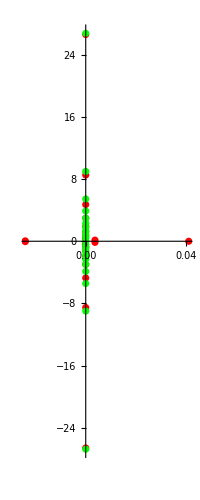

```mathematica
ComplexListPlot[{w[3],w[4]},PlotRange->All,PlotStyle->{Red,Green}]
```

```mathematica
w[1]=x/.NSolve[p[x]==0,x]
```

{0.0246233,0.217987,0.585786,1.09202,1.68713,2.31287,2.90798,3.41421,3.78201,3.97538}

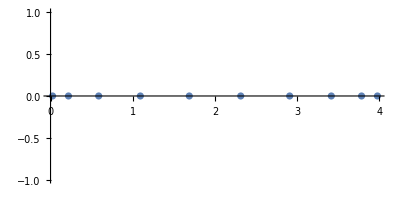

```mathematica
ComplexListPlot[w[1]]
```

```mathematica
w[2]=x/.NSolve[q[x]==0,x]
```

{2.-0.312869 ⅈ,2.+0.312869 ⅈ,2.-1.41421 ⅈ,2.+1.41421 ⅈ,2.-1.97538 ⅈ,2.+1.97538 ⅈ,2.-1.78201 ⅈ,2.+1.78201 ⅈ,2.-0.907981 ⅈ,2.+0.907981 ⅈ}

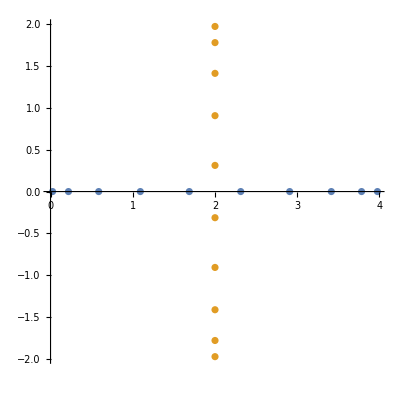

```mathematica
ComplexListPlot[{w[1],w[2]}]
```

```mathematica
B1010c=B10.B10c
```

{{3.29289+0.707107 ⅈ,-3.41421-1.41421 ⅈ,0.707107+0.707107 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{-0.585786-1.41421 ⅈ,4.+1.41421 ⅈ,-3.41421-1.41421 ⅈ,0.707107+0.707107 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{-0.707107+0.707107 ⅈ,-0.585786-1.41421 ⅈ,4.+1.41421 ⅈ,-3.41421-1.41421 ⅈ,0.707107+0.707107 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-0.707107+0.707107 ⅈ,-0.585786-1.41421 ⅈ,4.+1.41421 ⅈ,-3.41421-1.41421 ⅈ,0.707107+0.707107 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,-0.707107+0.707107 ⅈ,-0.585786-1.41421 ⅈ,4.+1.41421 ⅈ,-3.41421-1.41421 ⅈ,0.707107+0.707107 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-0.707107+0.707107 ⅈ,-0.585786-1.41421 ⅈ,4.+1.41421 ⅈ,-3.41421-1.41421 ⅈ,0.707107+0.707107 ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-0.707107+0.707107 ⅈ,-0.585786-1.41421 ⅈ,4.+1.41421 ⅈ,-3.41421-1.41421 ⅈ,0.707107+0.707107 ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-0.707107+0.707107 ⅈ,-0.585786-1.41421 ⅈ,4.+1.41421 ⅈ,-3.41421-1.41421 ⅈ,0.707107+0.707107 ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-0.707107+0.707107 ⅈ,-0.585786-1.41421 ⅈ,3.29289+2.12132 ⅈ,-3.41421-1.41421 ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-1.41421+1.41421 ⅈ,-1.17157-2.82843 ⅈ,5.41421+1.41421 ⅈ}}

```mathematica
WeightedAdjacencyGraph[B1010c]
```

-Graphics-

```mathematica
Det[B1010c]
```

13452.+2.45564×10^-11 ⅈ

```mathematica
Tr[B1010c]
```

40.+14.1421 ⅈ

```mathematica
u[3]=N[Eigenvalues[B1010c]]
```

{7.46772+6.82109 ⅈ,7.10903+5.72397 ⅈ,6.41894+3.85023 ⅈ,5.47846+1.66839 ⅈ,4.46647-0.365954 ⅈ,4.04141-1.64189 ⅈ,2.99233-1.02661 ⅈ,1.48279-0.589586 ⅈ,0.49134-0.263366 ⅈ,0.0515072-0.0341391 ⅈ}

```mathematica
s[x_]=CharacteristicPolynomial[B1010c,x]//Chop
```

13452.-(226344.+134138. ⅈ) x+(534001.+614538. ⅈ) x^2-(507000.+839873. ⅈ) x^3+(283178.+546905. ⅈ) x^4-(109448.+202190. ⅈ) x^5+(29983.+45232.2 ⅈ) x^6-(5544.+6086.78 ⅈ) x^7+(638.+452.548 ⅈ) x^8-(40.+14.1421 ⅈ) x^9+x^10

```mathematica
o[z_,3]=Integrate[s[x]^2,{x,-z,z}]
```

(0.+0. ⅈ)+3.61913×10^8 z+(3.17369×10^10+5.15042×10^10 ⅈ) z^3-(3.22746×10^10-4.74903×10^11 ⅈ) z^5-(2.34852×10^11-5.44538×10^11 ⅈ) z^7-(1.04498×10^11-1.75116×10^11 ⅈ) z^9-(1.19744×10^10-2.17165×10^10 ⅈ) z^11-(3.86243×10^8-1.1267×10^9 ⅈ) z^13-(718762.-2.30278×10^7 ⅈ) z^15+(62772.9+154314. ⅈ) z^17+(281.684+214.365 ⅈ) z^19+0.0952381 z^21

```mathematica
o[z_,4]=Integrate[p[x]*q[z],{x,-z,z}]
```

26904. z-95120. z^2+3.85556×10^6 z^3-1.32361×10^7 z^4+3.31347×10^7 z^5-6.24623×10^7 z^6+8.616×10^7 z^7-8.99962×10^7 z^8+7.4102×10^7 z^9-4.92927×10^7 z^10+2.67428×10^7 z^11-1.18478×10^7 z^12+4.28051×10^6 z^13-1.25921×10^6 z^14+300654. z^15-57668.2 z^16+8648.69 z^17-959.192 z^18+72.3232 z^19-3.63636 z^20+(2 z^21)/11

```mathematica
w[5]=z/.NSolve[o[z,4]==0,z]
```

{0.,0.-0.0862855 ⅈ,0.+0.0862855 ⅈ,0.-0.60244 ⅈ,0.+0.60244 ⅈ,0.-1.66712 ⅈ,0.+1.66712 ⅈ,0.-3.93552 ⅈ,0.+3.93552 ⅈ,0.-13.7528 ⅈ,0.+13.7528 ⅈ,2.-0.312869 ⅈ,2.+0.312869 ⅈ,2.-1.41421 ⅈ,2.+1.41421 ⅈ,2.-1.97538 ⅈ,2.+1.97538 ⅈ,2.-1.78201 ⅈ,2.+1.78201 ⅈ,2.-0.907981 ⅈ,2.+0.907981 ⅈ}

```mathematica
w[6]=z/.NSolve[o[z,3]-1==0,z]
```

{-18.6211+53.3881 ⅈ,-5.48499+17.5414 ⅈ,-2.53692+10.1567 ⅈ,-1.1671+6.76092 ⅈ,-0.417307+4.63937 ⅈ,-0.20171-0.979982 ⅈ,-0.172346-1.88733 ⅈ,-0.125403-0.361482 ⅈ,-0.0392905-0.068688 ⅈ,-0.0108126+3.08833 ⅈ,2.7631×10^-9,0.0108126-3.08833 ⅈ,0.0392905+0.068688 ⅈ,0.125403+0.361482 ⅈ,0.172346+1.88733 ⅈ,0.20171+0.979982 ⅈ,0.417307-4.63937 ⅈ,1.1671-6.76092 ⅈ,2.53692-10.1567 ⅈ,5.48499-17.5414 ⅈ,18.6211-53.3881 ⅈ}

```mathematica
(*root test as ones and zero*)
```

```mathematica
FullSimplify[Table[o[w[3][[j]],1],{j,Length[w[3]]}]]//Chop
```

{1.,1.,1.,1.,1.+1.11759×10^-8 ⅈ,1.-1.11759×10^-8 ⅈ,1.00002+0.000366211 ⅈ,1.00002-0.000366211 ⅈ,0.+0.0625 ⅈ,0.-0.0625 ⅈ,0.-6176. ⅈ,0.+6176. ⅈ,0.+9.24083×10^12 ⅈ,0.-9.24083×10^12 ⅈ,1.-1.90735×10^-6 ⅈ,1.+1.90735×10^-6 ⅈ,1.,1.,1.,1.,1.}

```mathematica
FullSimplify[Table[o[w[4][[j]],2],{j,Length[w[4]]}]]//Chop
```

{1.-9.30231×10^-9 ⅈ,1.+9.30231×10^-9 ⅈ,0.999997-3.33786×10^-6 ⅈ,0.999997+3.33786×10^-6 ⅈ,1.+0.000366211 ⅈ,1.-0.000366211 ⅈ,0.+0.125 ⅈ,0.-0.125 ⅈ,0.+1.5 ⅈ,0.-1.5 ⅈ,0.+26592. ⅈ,0.-26592. ⅈ,0.+7.67218×10^12 ⅈ,0.-7.67218×10^12 ⅈ,1.,1.,1.+7.62939×10^-6 ⅈ,1.-7.62939×10^-6 ⅈ,1.-4.84288×10^-8 ⅈ,1.+4.84288×10^-8 ⅈ,1.}

```mathematica
FullSimplify[Table[o[w[5][[j]],4],{j,Length[w[4]]}]]//Chop
```

{0,0,0,3.92902×10^-10-2.11003×10^-10 ⅈ,3.92902×10^-10+2.11003×10^-10 ⅈ,4.76837×10^-7+9.53674×10^-7 ⅈ,4.76837×10^-7-9.53674×10^-7 ⅈ,-0.0078125-0.046875 ⅈ,-0.0078125+0.046875 ⅈ,-2.39677×10^7+4.15334×10^7 ⅈ,-2.39677×10^7-4.15334×10^7 ⅈ,-9.53674×10^-7+3.8147×10^-6 ⅈ,-9.53674×10^-7-3.8147×10^-6 ⅈ,0.0000305176-0.0000915527 ⅈ,0.0000305176+0.0000915527 ⅈ,0.000244141+0.000366211 ⅈ,0.000244141-0.000366211 ⅈ,-0.0000610352+0.00012207 ⅈ,-0.0000610352-0.00012207 ⅈ,0.0000209808,0.0000209808}

```mathematica
FullSimplify[Table[o[w[6][[j]],3],{j,Length[w[6]]}]]//Chop
```

{-2.97267×10^20+7.83305×10^19 ⅈ,-2.18355×10^11+6.45818×10^11 ⅈ,-9.20781×10^6+5.91462×10^6 ⅈ,20992.+4096. ⅈ,88.+64. ⅈ,0.999759-0.000286102 ⅈ,1.01563-0.0078125 ⅈ,1.-1.22723×10^-6 ⅈ,1.+1.28898×10^-9 ⅈ,3.5+0.5 ⅈ,1.,-1.5-1. ⅈ,1.+3.49536×10^-9 ⅈ,0.999999-2.69312×10^-7 ⅈ,1.01563-0.00195313 ⅈ,0.999739+0.00062561 ⅈ,-8.+96. ⅈ,-38400.+22528. ⅈ,-8.2903×10^6+3.11296×10^6 ⅈ,7.59085×10^10-1.30503×10^11 ⅈ,2.97267×10^20-7.83305×10^19 ⅈ}

```mathematica
ph[x_,1]=x^2*q[x]/p[x]
```

(x^2 (6726.-23780. x+39065. x^2-39280. x^3+26790. x^4-12964. x^5+4515. x^6-1120. x^7+190. x^8-20. x^9+x^10))/(2-100 x+825 x^2-2640 x^3+4290 x^4-4004 x^5+2275 x^6-800 x^7+170 x^8-20 x^9+x^10)

```mathematica
ph[z_,2]=z^2*(o[z,2]-1)/(o[z,1]-1)
```

(z^2 (-1.+9.04782×10^7 z+7.27327×10^8 z^3+1.50184×10^9 z^5+1.23238×10^9 z^7+4.76608×10^8 z^9+9.34137×10^7 z^11+9.42371×10^6 z^13+472299. z^15+10580. z^17+82.1053 z^19+0.0952381 z^21))/(-1+8 z+(26600 z^3)/3+490314 z^5+(29716000 z^7)/7+9657700 z^9+7283640 z^11+2022750 z^13+(632896 z^15)/3+7700 z^17+(1480 z^19)/19+(2 z^21)/21)

```mathematica
g1=JuliaSetPlot[ph[x,1]/N[4],x,ColorFunction->Hue,ImageSize->2000,AspectRatio->1,ImageResolution->2000,PerformanceGoal->"Quality",Frame->False,Axes->False];
```

```mathematica
g2=ListPlot[JuliaSetPoints[ph[x,1]/N[4],x],ImageSize->2000,PlotStyle->{PointSize[0.001]},ColorFunction->Hue,PlotRange->All,AspectRatio->1];
```

```mathematica
Export["Julia_B_10_Hermanrings_scale4_both.jpg",{g1,g2}]
```

Julia_B_10_Hermanrings_scale4_both.jpg

```mathematica
(*end*)
```

#### 3D and plane Mandelbrots/ Julias

```mathematica
(*scaled Cartan SO(4) Group Sum  Herman rings*)
```

```mathematica
f[x_]=(x^2 (6726-23780*x+39065 *x^2-39280*x^3+26790*x^4-12964*x^5+4515*x^6-1120*x^7+190*x^8-20*x^9+x^10))/(2-100 x+825 x^2-2640 x^3+4290 x^4-4004 x^5+2275 x^6-800 x^7+170 x^8-20 x^9+x^10)
```

(x^2 (6726-23780 x+39065 x^2-39280 x^3+26790 x^4-12964 x^5+4515 x^6-1120 x^7+190 x^8-20 x^9+x^10))/(2-100 x+825 x^2-2640 x^3+4290 x^4-4004 x^5+2275 x^6-800 x^7+170 x^8-20 x^9+x^10)

```mathematica
(*Mandelbrot with SQRT(x^2+y^2) limited measure*)
(*by R. L. BAGULA 28 Nov 2026 © *)
numberOfz2ToEscape[z_] := Block[
	{escapeCount, nz = N[z],nzold=0},
	For[
		escapeCount = 0,
		(Sqrt[Re[nz]^2+Im[nz]^2] < 32) && (escapeCount < 1024) && (Abs[nz-nzold]>.5*10^(-3)),
		nzold=nz;
		nz=f[nz]/4.;
		++escapeCount
	];
	escapeCount*(1-Abs[Arg[nz]/(2*Pi)])
]
```

```mathematica
FractalPureM[{{ReMin_, ReMax_, ReSteps_},
			 {ImMin_, ImMax_, ImSteps_}}] :=
		ParallelTable[
			numberOfz2ToEscape[x + y I],
			{y, ImMin, ImMax, (ImMax - ImMin)/ImSteps},
			{x, ReMin, ReMax, (ReMax - ReMin)/ReSteps}
		
	]
```

```mathematica
arraym=FractalPureM[{{-6.500001,6.5,1000},{-6.5,6.5,1000}}];
```

```mathematica
g1=ListPlot3D[Log[1/Max[arraym]+arraym], Mesh -> False,AspectRatio -> 1,Boxed->False, Axes->False,ColorFunction->Hue,Background->Black,ViewPoint->Above,ImageSize->3000];
```

```mathematica
Export["j_1000_Cartan2_B_10_Hermanrings_scale4_Arg_Monitor_g1.jpg",g1]
```

j_1000_Cartan2_B_10_Hermanrings_scale4_Arg_Monitor_g1.jpg

```mathematica
arraym=FractalPureM[{{-6.500001,6.5,1500},{-6.5,6.5,1500}}];
```

```mathematica
g2=ListDensityPlot[Abs[Log[1+arraym]],Mesh -> False,AspectRatio -> 1,ColorFunction->"DarkRainbow",ImageSize->3000,Frame->False];
```

```mathematica
Export["j_1500_Cartan2_B_10_Hermanrings_scale4_Arg_Monitor_g2.jpg",g2]
```

j_1500_Cartan2_B_10_Hermanrings_scale4_Arg_Monitor_g2.jpg

```mathematica
g3=ListDensityPlot[arraym,Mesh -> False, AspectRatio -> 1, ColorFunction->"DarkBands",ImageSize->3000,Frame->False];
```

```mathematica
Export["j_1500__Cartan2_B_10_Hermanrings_scale4_Arg_Monitor_g3.jpg",g3]
```

j_1500__Cartan2_B_10_Hermanrings_scale4_Arg_Monitor_g3.jpg

```mathematica
g4=ListDensityPlot[arraym, Mesh -> False, AspectRatio -> 1,ColorFunction->(Hue[#]&),ImageSize->3000,Axes->False,Frame->False];
```

```mathematica
Export["j_1500_Cartan2_B_10_Hermanrings_scale4_Arg_Monitor_g4.jpg",g4]
```

j_1500_Cartan2_B_10_Hermanrings_scale4_Arg_Monitor_g4.jpg

```mathematica
g5=ListDensityPlot[Log[1/Max[arraym]+arraym],Mesh -> False, AspectRatio ->1, ColorFunction->(Hue[#*1.15]&),ImageSize->3000,Axes->False,Frame->False];
```

```mathematica
Export["j_1500_Cartan2_B_10_Hermanrings_scale4_Arg_Monitor_g5.jpg",g5]
```

j_1500_Cartan2_B_10_Hermanrings_scale4_Arg_Monitor_g5.jpg

```mathematica
(*Fonction pour colorier des isocontours,exemple d'utilisation typique:ContourPlot[T[x,y],{x,-10,10},{y,-10,10},ColorFunction->cf]*)
(*http://perso.ensem.inpl-nancy.fr/Emmanuel.Plaut/mathematica/mycolorfunction.m*)
colortab=Reverse[Union[Join[{{0,0,0.5625},{0,0,0.625},{0,0,0.6875},{0,0,0.75},{0,0,0.8125},{0,0,0.875},{0,0,0.9375},{0,0,1},{0,0.0625,1},{0,0.125,1},{0,0.1875,1},{0,0.25,1},{0,0.3125,1},{0,0.375,1},{0,0.4375,1},{0,0.5,1},{0,0.5625,1},{0,0.625,1},{0,0.6875,1},{0,0.75,1},{0,0.8125,1},{0,0.875,1},{0,0.9375,1},{0,1,1},{0.0625,1,1},{0.125,1,0.9375},{0.1875,1,0.875},{0.25,1,0.8125},{0.3125,1,0.75},{0.375,1,0.6875},{0.4375,1,0.625},{0.5,1,0.5625},{0.5625,1,0.5},{0.625,1,0.4375},{0.6875,1,0.375},{0.75,1,0.3125},{0.8125,1,0.25},{0.875,1,0.1875},{0.9375,1,0.125},{1,1,0.0625},{1,1,0},{1,0.9375,0},{1,0.875,0},{1,0.8125,0},{1,0.75,0},{1,0.6875,0},{1,0.625,0},{1,0.5625,0},{1,0.5,0},{1,0.4375,0},{1,0.375,0},{1,0.3125,0},{1,0.25,0},{1,0.1875,0},{1,0.125,0},{1,0.0625,0},{1,0,0},{0.9375,0,0},{0.875,0,0},{0.8125,0,0},{0.75,0,0},{0.6875,0,0},{0.625,0,0},{0.5625,0,0}},{{0,0,0.5625},{0,0,0.625},{0,0,0.6875},{0,0,0.75},{0,0,0.8125},{0,0,0.875},{0,0,0.9375},{0,0,1},{0,0.0625,1},{0,0.125,1},{0,0.1875,1},{0,0.25,1},{0,0.3125,1},{0,0.375,1},{0,0.4375,1},{0,0.5,1},{0,0.5625,1},{0,0.625,1},{0,0.6875,1},{0,0.75,1},{0,0.8125,1},{0,0.875,1},{0,0.9375,1},{0,1,1},{0.0625,1,1},{0.125,1,0.9375},{0.1875,1,0.875},{0.25,1,0.8125},{0.3125,1,0.75},{0.375,1,0.6875},{0.4375,1,0.625},{0.5,1,0.5625},{0.5625,1,0.5},{0.625,1,0.4375},{0.6875,1,0.375},{0.75,1,0.3125},{0.8125,1,0.25},{0.875,1,0.1875},{0.9375,1,0.125},{1,1,0.0625},{1,1,0},{1,0.9375,0},{1,0.875,0},{1,0.8125,0},{1,0.75,0},{1,0.6875,0},{1,0.625,0},{1,0.5625,0},{1,0.5,0},{1,0.4375,0},{1,0.375,0},{1,0.3125,0},{1,0.25,0},{1,0.1875,0},{1,0.125,0},{1,0.0625,0},{1,0,0},{0.9375,0,0},{0.875,0,0},{0.8125,0,0},{0.75,0,0},{0.6875,0,0},{0.625,0,0},{0.5625,0,0}}*1.25,{{0,0,0.5625},{0,0,0.625},{0,0,0.6875},{0,0,0.75},{0,0,0.8125},{0,0,0.875},{0,0,0.9375},{0,0,1},{0,0.0625,1},{0,0.125,1},{0,0.1875,1},{0,0.25,1},{0,0.3125,1},{0,0.375,1},{0,0.4375,1},{0,0.5,1},{0,0.5625,1},{0,0.625,1},{0,0.6875,1},{0,0.75,1},{0,0.8125,1},{0,0.875,1},{0,0.9375,1},{0,1,1},{0.0625,1,1},{0.125,1,0.9375},{0.1875,1,0.875},{0.25,1,0.8125},{0.3125,1,0.75},{0.375,1,0.6875},{0.4375,1,0.625},{0.5,1,0.5625},{0.5625,1,0.5},{0.625,1,0.4375},{0.6875,1,0.375},{0.75,1,0.3125},{0.8125,1,0.25},{0.875,1,0.1875},{0.9375,1,0.125},{1,1,0.0625},{1,1,0},{1,0.9375,0},{1,0.875,0},{1,0.8125,0},{1,0.75,0},{1,0.6875,0},{1,0.625,0},{1,0.5625,0},{1,0.5,0},{1,0.4375,0},{1,0.375,0},{1,0.3125,0},{1,0.25,0},{1,0.1875,0},{1,0.125,0},{1,0.0625,0},{1,0,0},{0.9375,0,0},{0.875,0,0},{0.8125,0,0},{0.75,0,0},{0.6875,0,0},{0.625,0,0},{0.5625,0,0}}/1.25,{{0,0,0.5625},{0,0,0.625},{0,0,0.6875},{0,0,0.75},{0,0,0.8125},{0,0,0.875},{0,0,0.9375},{0,0,1},{0,0.0625,1},{0,0.125,1},{0,0.1875,1},{0,0.25,1},{0,0.3125,1},{0,0.375,1},{0,0.4375,1},{0,0.5,1},{0,0.5625,1},{0,0.625,1},{0,0.6875,1},{0,0.75,1},{0,0.8125,1},{0,0.875,1},{0,0.9375,1},{0,1,1},{0.0625,1,1},{0.125,1,0.9375},{0.1875,1,0.875},{0.25,1,0.8125},{0.3125,1,0.75},{0.375,1,0.6875},{0.4375,1,0.625},{0.5,1,0.5625},{0.5625,1,0.5},{0.625,1,0.4375},{0.6875,1,0.375},{0.75,1,0.3125},{0.8125,1,0.25},{0.875,1,0.1875},{0.9375,1,0.125},{1,1,0.0625},{1,1,0},{1,0.9375,0},{1,0.875,0},{1,0.8125,0},{1,0.75,0},{1,0.6875,0},{1,0.625,0},{1,0.5625,0},{1,0.5,0},{1,0.4375,0},{1,0.375,0},{1,0.3125,0},{1,0.25,0},{1,0.1875,0},{1,0.125,0},{1,0.0625,0},{1,0,0},{0.9375,0,0},{0.875,0,0},{0.8125,0,0},{0.75,0,0},{0.6875,0,0},{0.625,0,0},{0.5625,0,0}}/2,{{0,0,0.5625},{0,0,0.625},{0,0,0.6875},{0,0,0.75},{0,0,0.8125},{0,0,0.875},{0,0,0.9375},{0,0,1},{0,0.0625,1},{0,0.125,1},{0,0.1875,1},{0,0.25,1},{0,0.3125,1},{0,0.375,1},{0,0.4375,1},{0,0.5,1},{0,0.5625,1},{0,0.625,1},{0,0.6875,1},{0,0.75,1},{0,0.8125,1},{0,0.875,1},{0,0.9375,1},{0,1,1},{0.0625,1,1},{0.125,1,0.9375},{0.1875,1,0.875},{0.25,1,0.8125},{0.3125,1,0.75},{0.375,1,0.6875},{0.4375,1,0.625},{0.5,1,0.5625},{0.5625,1,0.5},{0.625,1,0.4375},{0.6875,1,0.375},{0.75,1,0.3125},{0.8125,1,0.25},{0.875,1,0.1875},{0.9375,1,0.125},{1,1,0.0625},{1,1,0},{1,0.9375,0},{1,0.875,0},{1,0.8125,0},{1,0.75,0},{1,0.6875,0},{1,0.625,0},{1,0.5625,0},{1,0.5,0},{1,0.4375,0},{1,0.375,0},{1,0.3125,0},{1,0.25,0},{1,0.1875,0},{1,0.125,0},{1,0.0625,0},{1,0,0},{0.9375,0,0},{0.875,0,0},{0.8125,0,0},{0.75,0,0},{0.6875,0,0},{0.625,0,0},{0.5625,0,0}}/3,{{0,0,0.5625},{0,0,0.625},{0,0,0.6875},{0,0,0.75},{0,0,0.8125},{0,0,0.875},{0,0,0.9375},{0,0,1},{0,0.0625,1},{0,0.125,1},{0,0.1875,1},{0,0.25,1},{0,0.3125,1},{0,0.375,1},{0,0.4375,1},{0,0.5,1},{0,0.5625,1},{0,0.625,1},{0,0.6875,1},{0,0.75,1},{0,0.8125,1},{0,0.875,1},{0,0.9375,1},{0,1,1},{0.0625,1,1},{0.125,1,0.9375},{0.1875,1,0.875},{0.25,1,0.8125},{0.3125,1,0.75},{0.375,1,0.6875},{0.4375,1,0.625},{0.5,1,0.5625},{0.5625,1,0.5},{0.625,1,0.4375},{0.6875,1,0.375},{0.75,1,0.3125},{0.8125,1,0.25},{0.875,1,0.1875},{0.9375,1,0.125},{1,1,0.0625},{1,1,0},{1,0.9375,0},{1,0.875,0},{1,0.8125,0},{1,0.75,0},{1,0.6875,0},{1,0.625,0},{1,0.5625,0},{1,0.5,0},{1,0.4375,0},{1,0.375,0},{1,0.3125,0},{1,0.25,0},{1,0.1875,0},{1,0.125,0},{1,0.0625,0},{1,0,0},{0.9375,0,0},{0.875,0,0},{0.8125,0,0},{0.75,0,0},{0.6875,0,0},{0.625,0,0},{0.5625,0,0}}/4]]];
```

```mathematica
ln=Length[colortab]
```

380

```mathematica
cf[l_]:=Block[{niv,rgb},niv=If[l<1/ln,1,Ceiling[ln* l]];
rgb=colortab[[niv]];
RGBColor[rgb[[1]],rgb[[2]],rgb[[3]]]];
```

```mathematica
g6=ListDensityPlot[Log[1/Max[arraym]+arraym], Mesh -> False, AspectRatio -> 1, ColorFunction->cf,ImageSize->3000,Frame->False];
```

```mathematica
Export["j_1500_Cartan2_B_10_Hermanrings_scale4_Arg_Monitor_g6.jpg",g6]
```

j_1500_Cartan2_B_10_Hermanrings_scale4_Arg_Monitor_g6.jpg

```mathematica
Export["j_1500_Cartan2_B_10_Hermanrings_scale4_Arg_Monitor_grid.jpg",GraphicsGrid[{{g1,g2}, 
 {g3,g4},{g5,g6}},ImageSize->{6000,9000}]]
```

j_1500_Cartan2_B_10_Hermanrings_scale4_Arg_Monitor_grid.jpg

```mathematica
(*end*)
```